## Opakování

1.)

Vytvořte 4 vektory “a, b, c, d” (o délce 5) jejichž obsah bude generován pomocí funkcí Range a Table.
Se zvolenými vektory proveďte následující operace:

	1) Skalární součin (mezi vektory a, b) a vektorový součin (mezi vektory a, b, c, d)
	2) Vymažte poslední prvek v každém vektoru. Výsledek uložte do původních vektorů
	3) Nahraďte 3 prvek ve vektoru “a” číslem 3
	4) Spojte všechny vektory do jednoho, který se bude jmenovat “e”

2.)

Vytvořte matici “m”, která se bude skládat z vektorů a, b, c, d. Vytvořenou matici zobrazíte.

	1) Pro vytvořenou matici vypočítejte determinant
	2) Vytvořte transponovanou matici k matici “m”
	3) Vytvořte nulovou matici, která ma na diagonále čísla 3, 4, 3, 6
	4) Vytvořte matici pomocí funkce Table (3x3)

## Obsah hodiny

Tabulky (TableForm a Grid)

Při práci s vektory a maticemi je někdy výhodné zobrazovat výsledky v tabulkové podobě. K tomu slouží funkce TableForm, která pracuje obdobně jako funkce MatrixForm. Tato funkce však obsahuje také spoustu parametrů, které slouží k naformátování tabulkové podoby výsledků. Jako první argument je vložena vytvořená matice. V dalších argumentech funkce je styl samotné tabulky.

Vytvoření matice

```mathematica
matice = Table[i^j, {i,5},{j,5}];
```

Využití funkce TableForm pro vizualizaci matice.

```mathematica
TableForm[matice]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

TableForm má však mnoho parametrů, které ovlivňují zobrazení výsledků. Jednotlivé parametry se píší do hranatých závorek a jsou odděleny od vstupu čárkou. 
Parametr TableAlignments určuje zarovnání hodnot v tabulce (hodnoty např. : Center, Right, Left, Top, Bottom).

```mathematica
TableForm[matice, TableAlignments->Center]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

Parametr TableDepth určuje v jaké dimenzi se tabulka zobrazí.

```mathematica
TableForm[matice, TableDepth->1]
```

{1,1,1,1,1}
{2,4,8,16,32}
{3,9,27,81,243}
{4,16,64,256,1024}
{5,25,125,625,3125}

Parametr TableDirections jestli bude tabulka vypisována po sloupcích nebo po řádcích.

```mathematica
TableForm[matice, TableDirections->Row]
```

1 | 2 | 3 | 4 | 5
1 | 4 | 9 | 16 | 25
1 | 8 | 27 | 64 | 125
1 | 16 | 81 | 256 | 625
1 | 32 | 243 | 1024 | 3125

Parametr TableHeadings definuje hlavičku tabulky.

```mathematica
TableForm[matice, TableHeadings->{{"r1","r2","r3","r4","r5"},{"c1","c2","c3","c4","c5"}}]
```

| c1 | c2 | c3 | c4 | c5
r1 | 1 | 1 | 1 | 1 | 1
r2 | 2 | 4 | 8 | 16 | 32
r3 | 3 | 9 | 27 | 81 | 243
r4 | 4 | 16 | 64 | 256 | 1024
r5 | 5 | 25 | 125 | 625 | 3125

Parametr TableSpacing nastavuje mezery mezi sloupci a řádky.

```mathematica
TableForm[matice, TableSpacing->{4,4}]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

Využití několika parametru najednou

```mathematica
TableForm[matice, TableHeadings->{{"r1","r2","r3","r4","r5"},{"c1","c2","c3","c4","c5"}}, TableSpacing->{4,4},TableAlignments->Center]
```

| c1 | c2 | c3 | c4 | c5
r1 | 1 | 1 | 1 | 1 | 1
r2 | 2 | 4 | 8 | 16 | 32
r3 | 3 | 9 | 27 | 81 | 243
r4 | 4 | 16 | 64 | 256 | 1024
r5 | 5 | 25 | 125 | 625 | 3125

Funkce Grid

Grid je další funkcí pro zobrazení dat ve dvojrozměrném prostoru. Jako první argument funkce jsou vložena data (matice), další argumenty upravují zobrazení samotné tabulky.
Funkce grid umožňuje vykreslit mřížku

```mathematica
Grid[matice,Frame->All,FrameStyle->Purple]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

```mathematica
Grid[matice,Frame->{{Red,Purple,Green,Yellow,Pink},{Green,Black,Brown,Gray,Blue}}, Alignment->Right]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

Funkce Background vybarvuje pozadí tabulky.

```mathematica
Grid[matice,Frame->All,Background->LightBlue]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

Výpis čísla přez dvě buňky

```mathematica
Grid[{{1,2,3},{4,SpanFromLeft,6},{7,8,9}},Frame->All]
```

1 | 2 | 3
4 |  | 6
7 | 8 | 9

Kombinace funkce Grid a Table

```mathematica
Grid[matice,Frame->True]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

Další využití funkce Table ve funkci Grid.

```mathematica
Grid[matice,Background->{{{Yellow,None}},{{Purple,None}}}]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

Výběr a změna stylů určité podmožiny v tabulce pomocí funkce ItemStyle.

```mathematica
Grid[matice,ItemStyle->{Automatic,Automatic,{{{1,3},{1,3}}->Green}}]
```

1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

```mathematica
v=Prepend[matice,{"Col 1","Col 2","Col 3","Col 4","Col 5"}]
```

{{Col 1,Col 2,Col 3,Col 4,Col 5},{1,1,1,1,1},{2,4,8,16,32},{3,9,27,81,243},{4,16,64,256,1024},{5,25,125,625,3125}}

```mathematica
Grid[v]
```

Col 1 | Col 2 | Col 3 | Col 4 | Col 5
1 | 1 | 1 | 1 | 1
2 | 4 | 8 | 16 | 32
3 | 9 | 27 | 81 | 243
4 | 16 | 64 | 256 | 1024
5 | 25 | 125 | 625 | 3125

2D grafy - funkce Plot

Pro vykreslení grafů funkcí v rovině využívá Mathematica funkce Plot. 

V argumentu funkce Plot musí být zadána nejdříve vykreslovaná funkce a dále ve složených závorkách proměnná pro kterou je funkce vykreslována a meze této nezávislé proměnné, dále následuje výčet možného nastavení grafu (barvy, styl atd...nemusí být použito a graf je pak kreslen v základním nastavení).

Funkce Plot má opravdu hodně parametrů.

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

Základní zobrazení grafu pomocí funkce Plot



```mathematica
Plot[Sin[x],{x,0,2 π}]
```

Zobrazení několika grafů s vyplněnými plochami a mřížkou v jednom grafu s legendou.

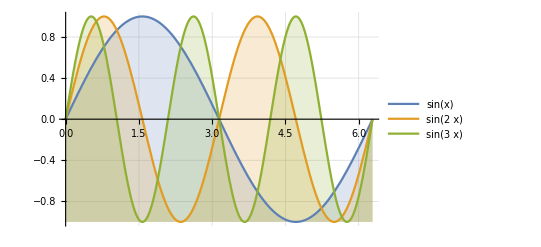

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2 π},PlotLegends->"Expressions",Filling->Bottom, GridLines->Automatic]
```

Popis grafu a os

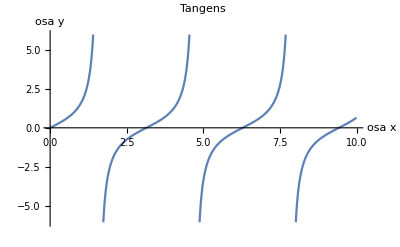

```mathematica
Plot[Tan[x],{x,0,10},AxesLabel->{"osa x","osa y"}, PlotLabel->"Tangens"]
```

Úprava vzhledu grafu je následující. Byl změněn poměr výšky a šířky, meze osy y, barvy pozadí grafu, parametr mřížky grafu, sloušťka a barva vykreslované křivky.

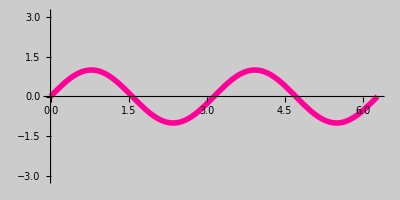

```mathematica
Plot[Sin[2x],{x,0,2π}, AspectRatio->1/2, PlotRange->{-π,π}, Background->GrayLevel[0.8], GridLines->{{0,π/2,π,3π/2,2π}, Automatic},PlotStyle->{Hue[0.9],Thickness[0.01]}]
```

## Samostatné úkoly

1.)

Vytvořte matici pomocí funkce Table (6x6).

	a) Využijte funkci TableForm pro vytvoření tabulky 
	b) Hodnoty v tabulce zarovnejte na střed, také popište jednotlivé sloupce (Sloupce od nadpisu oddělte čárou)
	c) Postup v bodě “b” opakujte jenom za využití funkce Grid (nezapomeňte na rozdílnost funkcí Grid a TableForm)
	d) Vytvořte tabulku pomocí funkce Grid a vytvořené matice, kde každý sudý sloupec má fialovou barvu v pozadí a liché sloupce mají bílou barvu pozadí.

2.)

Vytvořte Graf y=1/x, kde x spadá do intervalu (-1,1) za pomocí funkce Plot. 
	a) Popiště osy grafu a pojmenu tento graf.
	b) Vložte mřížku do grafu
	c) Změňte šířku křivky vykresleného grafu na 0.02.